# Quark Propagator DSE: Self-Energy diagram with ALL the tensor structures

## Dirac Vector Part -> A(p^2)

### Collecting coefficients after analyzing the tensor structure

After completing the several integrations by hand, we define the general momentum integral in terms of different powers in q^2 with the respective coefficients.

```mathematica
Clear[p, λA, λ, x]
```

```mathematica
(*vector part*)
A0[p_,λA_,x_] := 2(p^2/λA^2)*x^2  + 3x - 1
A1[p_,λA_,x_] := 1/(2λA^2)

AVec[p_,λA_,x_]:={A0[p,λA,x],A1[p,λA,x]}

B0[p_,λA_,x_] := 2(p^2/λA^2)*x^2 
B1[p_,λA_,x_] := 1/(2*λA^2)

BVec[p_,λA_,x_]:={B0[p,λA,x],B1[p,λA,x]}
```

I checked that we do not get any new corrections in any of the coefficients depending on d after expanding in d=4-2ϵ ..

### Perform momentum integration and collect coefficients for Feynman parameter integration

```mathematica
Clear[μ, p,λA,λ]
```

Checking the prefactors :

```mathematica
FullSimplify[Series[μ^(2ϵ)*(4π)^(ϵ-2)*Gamma[ϵ]* Δ^(-ϵ),{ϵ,0,0}]*16π^2]
```

1/ϵ+(-EulerGamma+Log[4]+Log[π]-Log[Δ]+2 Log[μ])+O[ϵ]^1

```mathematica
FullSimplify[Series[((4-2ϵ)/(2ϵ-2)), {ϵ,0,0}]]
```

-2+O[ϵ]^1

```mathematica
FullSimplify[Series[μ^(2ϵ)*(4π)^(ϵ-2)*((4-2ϵ)/(2ϵ-2))*Gamma[ϵ]* Δ^(-ϵ+1),{ϵ,0,0}]/(-2)*(16π^2)/Δ]
```

1/ϵ+(1/2-EulerGamma+Log[4]+Log[π]-Log[Δ]+2 Log[μ])+O[ϵ]^1

```mathematica
Δ1[psq_, λAsq_, λsq_, x_] := x(1-x)psq + (1-x)λAsq + x*λsq
Δ2[psq_, λsq_, x_] := Δ1[psq, 0, λsq, x]
```

```mathematica
(*vector part*)
α0[p_,λA_,λ_]:=Evaluate[FullSimplify[(A0[p,λA,x]-2*A1[p,λA,x]Δ1[p^2,λA^2,λ^2,x])/.x->0]]
α1[p_,λA_,λ_]:=Evaluate[FullSimplify[Coefficient[(A0[p,λA,x]-2*A1[p,λA,x]Δ1[p^2,λA^2,λ^2,x]),x]]]
α2[p_,λA_,λ_]:=Evaluate[FullSimplify[Coefficient[(A0[p,λA,x]-2*A1[p,λA,x]Δ1[p^2,λA^2,λ^2,x]),x^2]]]

β0[p_,λA_,λ_]:=Evaluate[FullSimplify[(B0[p,λA,x]-2*B1[p,λA,x]Δ2[p^2,λ^2,x])/.x->0]]
β1[p_,λA_,λ_]:=Evaluate[FullSimplify[Coefficient[(B0[p,λA,x]-2*B1[p,λA,x]Δ2[p^2,λ^2,x]),x]]]
β2[p_,λA_,λ_]:=Evaluate[FullSimplify[Coefficient[(B0[p,λA,x]-2*B1[p,λA,x]Δ2[p^2,λ^2,x]),x^2]]]

α[p_,λA_,λ_] := {α0[p,λA,λ],α1[p,λA,λ],α2[p,λA,λ]}
β[p_,λA_,λ_] := {β0[p,λA,λ],β1[p,λA,λ],β2[p,λA,λ]}
```

```mathematica
α[p,λA,λ]
```

{-2,-(p^2+λ^2-4 λA^2)/λA^2,(3 p^2)/λA^2}

```mathematica
β[p,λA,λ]
```

{0,-(p^2+λ^2)/λA^2,(3 p^2)/λA^2}

```mathematica
FullSimplify[Sum[(α[p,λA,λ][[i]]-β[p,λA,λ][[i]])/i,{i,3}]](*/.{λA->0,λ->0,p->ⅈ*ω}*)
```

0

```mathematica
Integrate[A1[p,λA,x]Δ1[p^2, λA^2, λ^2, x],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

1/4+p^2/(12 λA^2)+λ^2/(4 λA^2)

```mathematica
Integrate[B1[p,λA,x]Δ2[p^2,λ^2, x],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

p^2/(12 λA^2)+λ^2/(4 λA^2)

```mathematica
FullSimplify[1/4+p^2/(12 λA^2)+λ^2/(4 λA^2) - p^2/(12 λA^2)-λ^2/(4 λA^2)]
```

1/4

```mathematica
AdditionalTerm= 1/4
```

1/4

### Perform Feynman integrals and collect results

#### Order x^0

```mathematica
Integrate[Log[Δ1[p^2, λA^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

-2+Log[λ]+(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])/p^2+Log[λA]

```mathematica
Integrate[Log[Δ2[p^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

-2+(λ^2 Log[1+p^2/λ^2])/p^2+Log[p^2+λ^2]

```mathematica
f0[p_,λA_,λ_] := -2+Log[λ]+1/p^2(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])+Log[λA]
g0[p_,λA_,λ_] := -2+(λ^2 Log[1+p^2/λ^2])/p^2+Log[p^2+λ^2]
```

#### Order x^1

```mathematica
Integrate[x*Log[Δ1[p^2, λA^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

1/(4 p^4)(-4 p^4-2 p^2 λ^2+2 p^2 λA^2+2 (p^4-2 p^2 λ^2-(λ^2-λA^2)^2) Log[λ]+2 p^4 Log[λA]+4 p^2 λ^2 Log[λA]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])

```mathematica
Integrate[x*Log[Δ2[p^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

(-(2 p^2+λ^2) (p^2+2 λ^2 Log[λ])+(p^2+λ^2)^2 Log[p^2+λ^2])/(2 p^4)

```mathematica
f1[p_,λA_,λ_] := 1/(4 p^4)(-4 p^4-2 p^2 λ^2+2 p^2 λA^2+2 (p^4-2 p^2 λ^2-(λ^2-λA^2)^2) Log[λ]+2 p^4 Log[λA]+4 p^2 λ^2 Log[λA]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+p^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])
g1[p_,λA_,λ_] := (-(2 p^2+λ^2) (p^2+2 λ^2 Log[λ])+(p^2+λ^2)^2 Log[p^2+λ^2])/(2 p^4)
```

```mathematica
FullSimplify[f1[p,λA,λ]]
```

1/(4 p^4)(-2 p^2 (2 p^2+λ^2-λA^2)+2 (p^4-2 p^2 λ^2-(λ^2-λA^2)^2) Log[λ]+2 ((p^2+λ^2)^2-2 λ^2 λA^2+λA^4) Log[λA]-(p^2+λ^2-λA^2) √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) (Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]))

#### Order x^2

```mathematica
Integrate[x^2*Log[Δ1[p^2, λA^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

1/(18 p^6)(-13 p^6-15 p^4 λ^2-6 p^2 λ^4+3 p^4 λA^2+12 p^2 λ^2 λA^2-6 p^2 λA^4+6 (p^6-3 p^4 λ^2-(λ^2-λA^2)^3-3 p^2 (λ^4-λ^2 λA^2)) Log[λ]+6 p^6 Log[λA]+18 p^4 λ^2 Log[λA]+18 p^2 λ^4 Log[λA]+6 λ^6 Log[λA]-18 p^2 λ^2 λA^2 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])

```mathematica
Integrate[x^2*Log[Δ2[p^2, λ^2, x]],{x,0,1},Assumptions -> p>0 && λ>0 && λA>0]
```

-(13 p^6+15 p^4 λ^2+6 p^2 λ^4+12 (3 p^4 λ^2+3 p^2 λ^4+λ^6) Log[λ]-6 (p^2+λ^2)^3 Log[p^2+λ^2])/(18 p^6)

```mathematica
f2[p_,λA_,λ_] := 1/(18 p^6)(-13 p^6-15 p^4 λ^2-6 p^2 λ^4+3 p^4 λA^2+12 p^2 λ^2 λA^2-6 p^2 λA^4+6 (p^6-3 p^4 λ^2-(λ^2-λA^2)^3-3 p^2 (λ^4-λ^2 λA^2)) Log[λ]+6 p^6 Log[λA]+18 p^4 λ^2 Log[λA]+18 p^2 λ^4 Log[λA]+6 λ^6 Log[λA]-18 p^2 λ^2 λA^2 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2+λ^2-λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[-p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 p^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+6 p^2 λ^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λ^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-3 p^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]-6 λ^2 λA^2 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))]+3 λA^4 √(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2)) Log[p^2-λ^2+λA^2+√(p^4+(λ^2-λA^2)^2+2 p^2 (λ^2+λA^2))])
g2[p_,λA_,λ_] := -(13 p^6+15 p^4 λ^2+6 p^2 λ^4+12 (3 p^4 λ^2+3 p^2 λ^4+λ^6) Log[λ]-6 (p^2+λ^2)^3 Log[p^2+λ^2])/(18 p^6)
```

```mathematica
FullSimplify[f2[p,λA,λ]]
```

1/(18 p^6)(-p^2 (13 p^4+6 (λ^2-λA^2)^2+3 p^2 (5 λ^2-λA^2))+6 (p^6-3 p^4 λ^2-(λ^2-λA^2)^3+3 p^2 λ^2 (-λ^2+λA^2)) Log[λ]+6 (p^2+λ^2-λA^2) ((p^2+λ^2)^2+(p^2-2 λ^2) λA^2+λA^4) Log[λA]-3 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ((p^2+λ^2)^2-(p^2+2 λ^2) λA^2+λA^4) (Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]))

#### Storing the results

```mathematica
f[p_,λA_,λ_] := {f0[p,λA,λ],f1[p,λA,λ],f2[p,λA,λ]}
g[p_,λA_,λ_] := {g0[p,λA,λ],g1[p,λA,λ],g2[p,λA,λ]}
```

### Realtime Expressions

We first rewrite all hyperbolic functions in terms of logarithms (ArcCoth(x) = 1/2 * Log(x+1/x-1)) and use lim_ϵ->0+ log(x+iϵ) = log(x) + iπ θ(-x) to perform the correct continuation.

#### f0 and g0

```mathematica
f0Logs[p_,λA_,λ_] := -2+Log[λ]+ Log[λA] +1/(2 p^2)(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) (Log[1+1/((p^2+λ^2+λA^2)/√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))] - Log[1-1/((p^2+λ^2+λA^2)/√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))] )+2(-λ^2+λA^2) Log[λ/λA])
```

Compare if f0 and f0Log are the same :

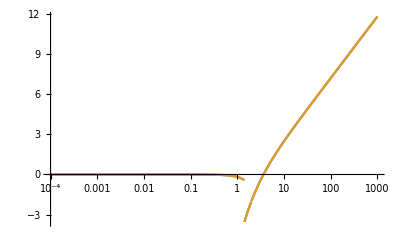

```mathematica
With[{λA=1,λ=1},LogLinearPlot[{Re[f0[-ⅈ*p,λA,λ]],Re[f0Logs[-ⅈ*p,λA,λ]]},{p,10^-4,10^3},WorkingPrecision->100,PlotRange->All]]
```

```mathematica
f0cont[ω_,λA_,λ_]:=f0Logs[-ⅈ ω,λA,λ]
g0cont[ω_,λA_,λ_]:=Conjugate[g0[-ⅈ*ω,λA,λ]]
```

#### Plots for f0 and g0

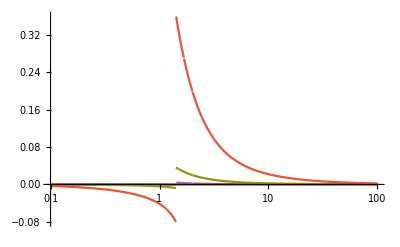

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[f0cont[ω,1,1]],Evaluate[Im[f0Logs[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-1,10^2},WorkingPrecision->30, PlotRange->All]},ImageSize->800]]
```

There seems to be some pole .. I used now the official definition of Mathematica for the ArcCoth und everything seems fine, also the continuation of the whole diagram works perfectly as displayed below.

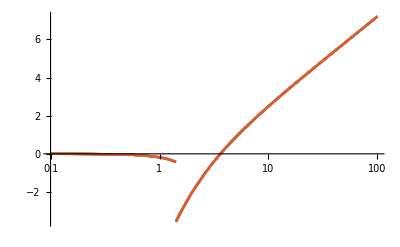

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[f0cont[ω,1,1]],Evaluate[Re[f0Logs[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-1,10^2},WorkingPrecision->30]},ImageSize->800]]
```

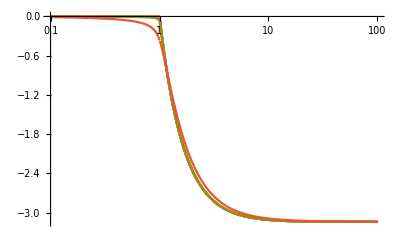

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[g0cont[ω,1,1]],Evaluate[Im[g0[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-1,10^2},WorkingPrecision->30]},ImageSize->800]]
```

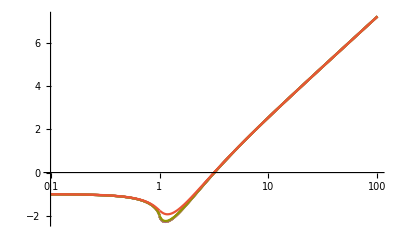

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[g0cont2[ω,1,1]],Evaluate[Re[g0[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-1,10^2},WorkingPrecision->30]},ImageSize->800]]
```

#### f1 and g1

```mathematica
f1cont[ω_,λA_,λ_] := f1[-ⅈ ω,λA,λ] (*Seems to work*)
g1cont[ω_,λA_,λ_] := Conjugate[g1[-ⅈ ω,λA,λ]] (*Check sign flip in real part*)
```

#### Plots for f1 and g1

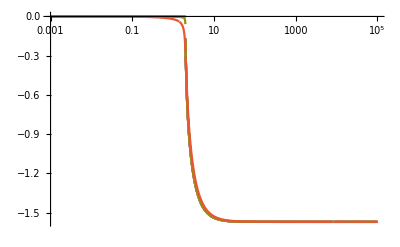

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[f1cont[ω,1,1]],Evaluate[Im[f1[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

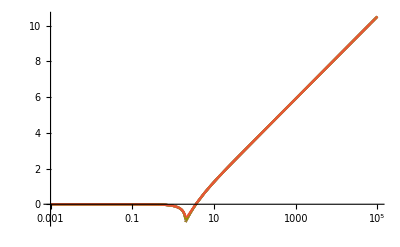

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[f1cont[ω,1,1]],Evaluate[Re[f1[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

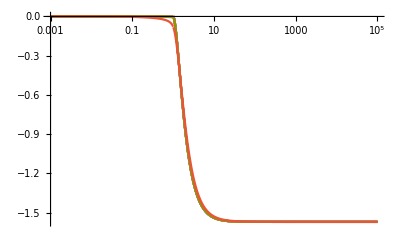

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[g1cont[ω,1,1]],Evaluate[Im[g1[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

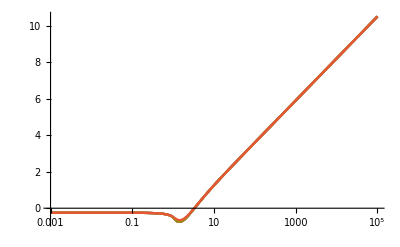

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[g1cont[ω,1,1]],Evaluate[Re[g1[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

#### f2 and g2

```mathematica
f2cont[ω_,λA_,λ_] := f2[-ⅈ ω,λA,λ] (*Seems to work*)
g2cont[ω_,λA_,λ_] := Conjugate[g2[-ⅈ ω,λA,λ]] (*Check sign flip in real part*)
```

#### Plots for f2 and g2

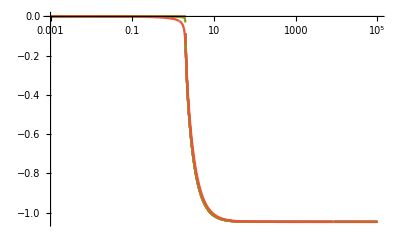

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[f2cont[ω,1,1]],Evaluate[Im[f2[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

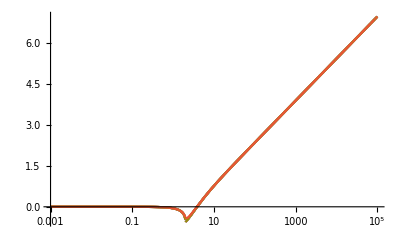

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[f2cont[ω,1,1]],Evaluate[Re[f2[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

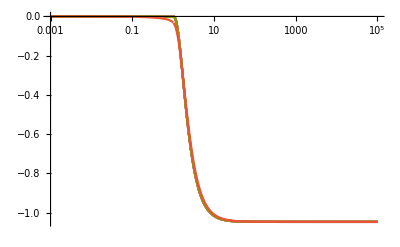

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[g2cont[ω,1,1]],Evaluate[Im[g2[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

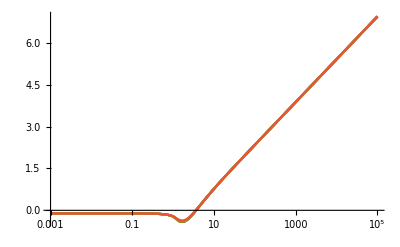

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Re[g2cont[ω,1,1]],Evaluate[Re[g2[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-3,10^5},WorkingPrecision->30]},ImageSize->800]]
```

#### Storing the results

```mathematica
fcont[ω_,λA_,λ_] := {f0cont[ω,λA,λ],f1cont[ω,λA,λ],f2cont[ω,λA,λ]}
gcont[ω_,λA_,λ_] := {g0cont[ω,λA,λ],g1cont[ω,λA,λ],g2cont[ω,λA,λ]}
```

### BPHZ Renormalization Scheme + Visualization

#### Plots etc.

Here we visualize the renormalization procedure for our spectral integrands. From a naive determination of the degree of divergence of our diagram we see that it should be log-divergent. For the spectral integration to be finite, the integrand has to go like λ^-2. We show some plots that in our case we alredy renormalized all the integrands by subtracting the lowest order term of our expansion around the renormalization scale μ.

```mathematica
β[1,1,λ]
```

{0,-1-λ^2,3}

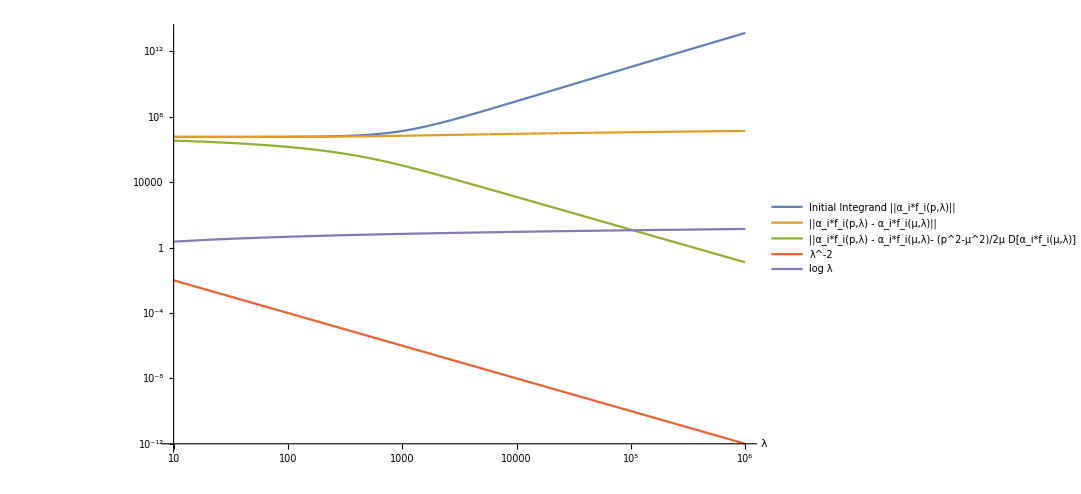

```mathematica
With[{λA=1, μ=10,pEval=1000, i=2},LogLogPlot[{Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]],Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[α[q,λA,λ][[i]]f[q, λA,λ][[i]],q]/.{q->μ})], λ^-2,  Log[λ]},{λ,10^1,10^6},WorkingPrecision->100, ImageSize->800 , PlotLegends->{"Initial Integrand ||α_i*f_i(p,λ)||", "||α_i*f_i(p,λ) - α_i*f_i(μ,λ)||", "||α_i*f_i(p,λ) - α_i*f_i(μ,λ)- (p^2-μ^2)/2μ D[α_i*f_i(μ,λ)] ||","λ^-2","log λ"}, AxesLabel->{"λ"}]]
```

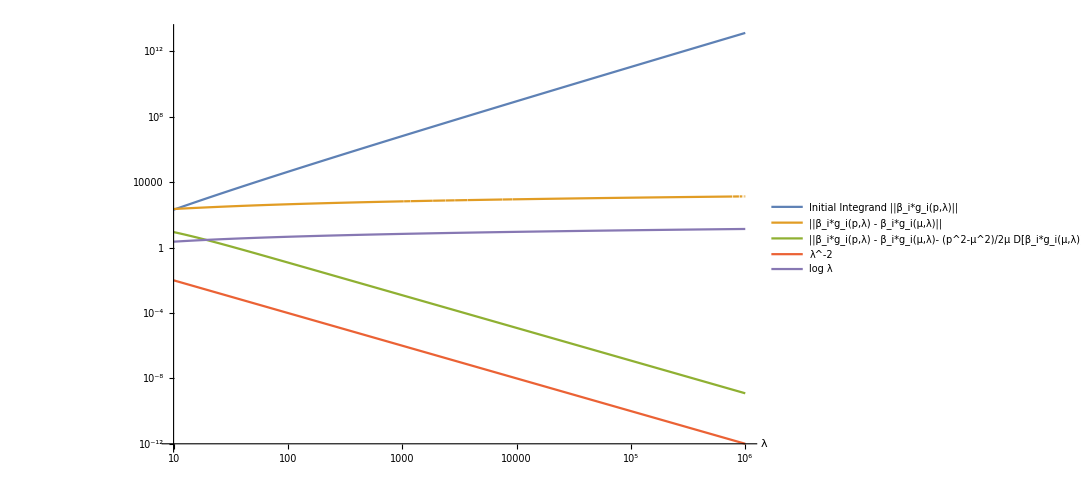

```mathematica
With[{λA=1, μ=10,pEval=1, i=2},LogLogPlot[{Abs[β[pEval,λA,λ][[i]]g[pEval,λA,λ][[i]]],Abs[β[pEval,λA,λ][[i]]g[pEval,λA,λ][[i]] - β[μ,λA,λ][[i]]g[μ, λA,λ][[i]]],Abs[β[pEval,λA,λ][[i]]g[pEval,λA,λ][[i]] - β[μ,λA,λ][[i]]g[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[β[q,λA,λ][[i]]g[q, λA,λ][[i]],q]/.{q->μ})], λ^-2,  Log[λ]},{λ,10^1,10^6},WorkingPrecision->100, ImageSize->800 , PlotLegends->{"Initial Integrand ||β_i*g_i(p,λ)||", "||β_i*g_i(p,λ) - β_i*g_i(μ,λ)||", "||β_i*g_i(p,λ) - β_i*g_i(μ,λ)- (p^2-μ^2)/2μ D[β_i*g_i(μ,λ)] ||","λ^-2","log λ"}, AxesLabel->{"λ"}]]
```

Check for explicit deviation of expected λ^-2 scaling :

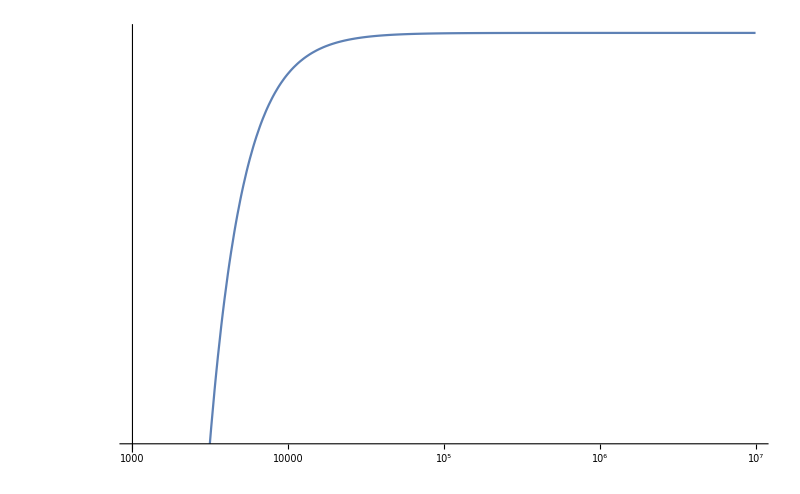

```mathematica
With[{λA=1, μ=100,pEval=1, i=2},LogLogPlot[{(Abs[α[pEval,λA,λ][[i]]f[pEval,λA,λ][[i]] - α[μ,λA,λ][[i]]f[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[α[q,λA,λ][[i]]f[q, λA,λ][[i]],q]/.{q->μ})])*λ^2},{λ,10^3,10^7},WorkingPrecision->150, ImageSize->800]]
```

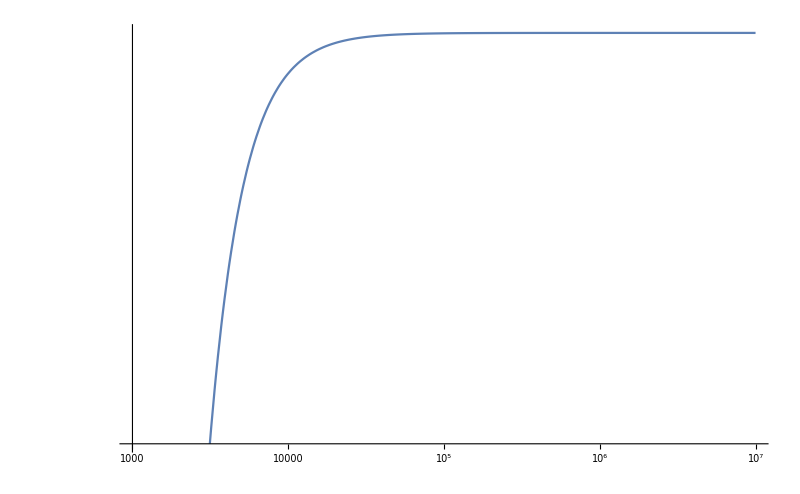

```mathematica
With[{λA=1, μ=100,pEval=1, i=2},LogLogPlot[{(Abs[β[pEval,λA,λ][[i]]g[pEval,λA,λ][[i]] - β[μ,λA,λ][[i]]g[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[β[q,λA,λ][[i]]g[q, λA,λ][[i]],q]/.{q->μ})])*λ^2},{λ,10^3,10^7},WorkingPrecision->150, ImageSize->800]]
```

This allows us to determine the upper limit on λ for the numerical integration later on!

#### Storing the renormalized integrands

Here we store the renormalized integrands after checking which terms have to be subtracted individually above.

```mathematica
(*NOT NEEDED, but I keep it here for comparison*)
αfRen[p_,λA_,λ_,μ_] := {α0[p,λA,λ]f0[p,λA,λ]-α0[μ,λA,λ]f0[μ,λA,λ],α1[p,λA,λ]f1[p,λA,λ]-α1[μ,λA,λ]f1[μ,λA,λ] - (p^2-μ^2)/(2μ)*(D[α1[q,λA,λ]f1[q, λA,λ],q]/.{q->μ}),α2[p,λA,λ]f2[p,λA,λ]-α2[μ,λA,λ]f2[μ,λA,λ] - (p^2-μ^2)/(2μ)*(D[α2[q,λA,λ]f2[q, λA,λ],q]/.{q->μ})}
βgRen[p_,λA_,λ_,μ_] := {β0[p,λA,λ]g0[p,λA,λ]-β0[μ,λA,λ]g0[μ,λA,λ],β1[p,λA,λ]g1[p,λA,λ]-β1[μ,λA,λ]g1[μ,λA,λ] - (p^2-μ^2)/(2μ)*(D[β1[q,λA,λ]g1[q, λA,λ],q]/.{q->μ}),β2[p,λA,λ]g2[p,λA,λ]-β2[μ,λA,λ]g2[μ,λA,λ]- (p^2-μ^2)/(2μ)*(D[β2[q,λA,λ]g2[q, λA,λ],q]/.{q->μ})}
```

#### Checking convergence of the spectral integrations (UV limit)

This is the expected UV behavior of the spectral functions :

```mathematica
ρ12UV[λ_] := 1/λ
ρAUV[λA_] := 1/λA^2
```

This gives the following integrands :

```mathematica
λIntRenTest1[pEval_,λA_, λ_, μ_,i_] :=  λ*ρ12UV[λ]* αfRen[pEval, λA,λ,μ][[i]]
λIntRenTest2[pEval_,λA_, λ_, μ_,i_] :=  λ*ρ12UV[λ]* βgRen[pEval, λA,λ,μ][[i]]

λIntRenTest[pEval_,λA_, λ_, μ_,i_] :=  λ*ρ12UV[λ]* (αfRen[pEval, λA,λ,μ][[i]] - βgRen[pEval, λA,λ,μ][[i]])
```

We test the integration for a set of different UV cutoffs:

```mathematica
UVCutoffs = 10^Range[2,8]
```

{100,1000,10000,100000,1000000,10000000,100000000}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {156249.5909378967244222130492718258162948372107884742130835697600888155007358951400449871226845691527}. NIntegrate obtained -478492.960394877689763618924738523816178471416664220282857953999404293642916657978193540603104073304 and 1.268989730711309085090050756693029969335854181984780632201809771612846644447277668209695495198587595×10^-74 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {2.167964582835960919257459941070727080937384754310217566053131130583768712308483516175754988153370182×10^6}. NIntegrate obtained -478507.9573950054930936855707494517413792917194523570698176112437821111950974706453539822333809367022 and 2.09831649743925174417476204419207561612821213708071267901957490375751640453114342611542317172961007×10^-72 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.01}. NIntegrate obtained -478509.4570950204708970155714049228533520842614032306828169043402295153612565162732480706168914858093 and 9.777256545392823193034820137481237751983574786212322396600500590783172372281586785925171093453461357×10^-66 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{100,-329284.823835121039291180492692092660382589973312051862347428259641303252221823597259892958895755655},{1000,-461868.4427302260021392621280510752843854822227595496056201075028574252762437300496878700938090737845},{10000,-476843.3125965778092031793774580977332636925116883786487388790514039502544724999869615986835478417891},{100000,-478342.9904155743530979216254852282469865767262484243578375475109529894792140063114808894649589562234},{1000000,-478492.960394877689763618924738523816178471416664220282857953999404293642916657978193540603104073304},{10000000,-478507.9573950054930936855707494517413792917194523570698176112437821111950974706453539822333809367022},{100000000,-478509.4570950204708970155714049228533520842614032306828169043402295153612565162732480706168914858093}}

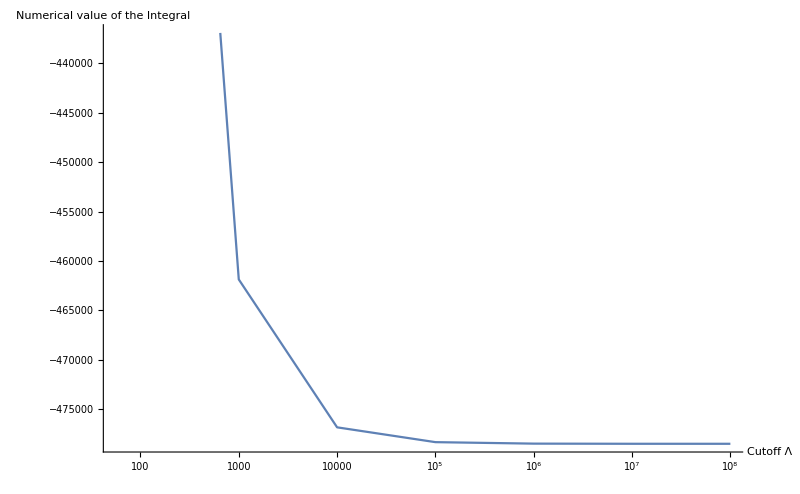

```mathematica
UVTest = With[{λA=1, pEval = 1, μ=100, i=3, λmin=10^-2},Table[{Λ,NIntegrate[λIntRenTest2[pEval,λA,λ,μ,i],{λ,λmin,Λ}, WorkingPrecision->100]},{Λ,UVCutoffs}]]
ListLogLinearPlot[UVTest,Joined ->True, ImageSize->800, AxesLabel->{"Cutoff Λ","Numerical value of the Integral"},PlotLabel->None,LabelStyle->{14}]
```

### Complete Diagram (Vector)

```mathematica
Clear[p,αs,λA,λ,μ]
```

Cf = (N^2 - 1)/(2N) = 4/3 for SU(3) + we get a factor of 8 from the contraction of the color factor δ^(ab).

```mathematica
IVecE[p_,αs_,λA_,λ_,μ_]:=-(32*αs)/(3(4π))(Sum[Log[4π*μ^2Exp[-EulerGamma]]*(α[p,λA,λ][[i]]-β[p,λA,λ][[i]])/i-α[p,λA,λ][[i]]*f[p,λA,λ][[i]]+β[p,λA,λ][[i]]*g[p,λA,λ][[i]],{i,3}] - AdditionalTerm)
IVecCont[ω_,αs_,λA_,λ_,μ_]:=-(32*αs)/(3(4π))(Sum[Log[4π*μ^2Exp[-EulerGamma]]*(α[-ⅈ ω,λA,λ][[i]]-β[-ⅈ ω,λA,λ][[i]])/i-α[-ⅈ ω,λA,λ][[i]]*fcont[ω,λA,λ][[i]]+β[-ⅈ ω,λA,λ][[i]]*gcont[ω,λA,λ][[i]],{i,3}] - AdditionalTerm)
DIVecE[p_,αs_,λA_,λ_,μ_]:=Evaluate[D[IVecE[p,αs,λA,λ,μ],p]]
```

```mathematica
IVecCont[ω,αs,λA,λ,μ]
```

-1/(3 π)8 αs (-1/4-((λ^2-ω^2) Conjugate[(-λ^2+2 ω^2) (-ω^2+2 λ^2 Log[λ])+(λ^2-ω^2)^2 Log[λ^2-ω^2]])/(2 λA^2 Conjugate[ω]^4)-(ω^2 (-13 Conjugate[ω]^6+Conjugate[-6 λ^4 ω^2+15 λ^2 ω^4+12 (λ^6-3 λ^4 ω^2+3 λ^2 ω^4) Log[λ]-6 (λ^2-ω^2)^3 Log[λ^2-ω^2]]))/(6 λA^2 Conjugate[ω]^6)-2 Log[4 ⅇ^-EulerGamma π μ^2]+1/2 ((λ^2-ω^2)/λA^2-(λ^2-4 λA^2-ω^2)/λA^2) Log[4 ⅇ^-EulerGamma π μ^2]+1/(4 λA^2 ω^4)(λ^2-4 λA^2-ω^2) (2 λ^2 ω^2-2 λA^2 ω^2-4 ω^4+2 (-(λ^2-λA^2)^2+2 λ^2 ω^2+ω^4) Log[λ]+2 λ^4 Log[λA]-4 λ^2 λA^2 Log[λA]+2 λA^4 Log[λA]-4 λ^2 ω^2 Log[λA]+2 ω^4 Log[λA]+λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-λ^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)])-1/(6 λA^2 ω^4)(6 λ^4 ω^2-12 λ^2 λA^2 ω^2+6 λA^4 ω^2-15 λ^2 ω^4+3 λA^2 ω^4+13 ω^6+6 (-(λ^2-λA^2)^3+3 (λ^4-λ^2 λA^2) ω^2-3 λ^2 ω^4-ω^6) Log[λ]+6 λ^6 Log[λA]-18 λ^4 λA^2 Log[λA]+18 λ^2 λA^4 Log[λA]-6 λA^6 Log[λA]-18 λ^4 ω^2 Log[λA]+18 λ^2 λA^2 ω^2 Log[λA]+18 λ^2 ω^4 Log[λA]-6 ω^6 Log[λA]+3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2-ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[λ^2-λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λ^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 λA^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]+6 λ^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 λA^2 ω^2 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)]-3 ω^4 √((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4) Log[-λ^2+λA^2+ω^2+√((λ^2-λA^2)^2-2 (λ^2+λA^2) ω^2+ω^4)])+2 (-2+Log[λ]+Log[λA]-(2 (-λ^2+λA^2) Log[λ/λA]+√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2) (-Log[1-(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2))/(λ^2+λA^2-ω^2)]+Log[1+(√(λA^4+2 λA^2 (-λ-ⅈ ω) (λ-ⅈ ω)+(λ^2-ω^2)^2))/(λ^2+λA^2-ω^2)]))/(2 ω^2)))

```mathematica
FullSimplify[%1915]
```

1/(3 p^4 π λA^2)2 αs (p^2 λA^2 (p^2-2 λ^2+4 λA^2)-8 p^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+2 ((p^2+λ^2)^3-4 p^2 λ^2 λA^2+(p^2+3 λ^2) λA^4-2 λA^6) Log[λ]-2 (p^2+λ^2)^3 Log[p^2+λ^2]+8 p^2 (λ-λA) λA^2 (λ+λA) Log[λ/λA]+2 ((p^2+λ^2)^3+4 p^2 λ^2 λA^2-(p^2+3 λ^2) λA^4+2 λA^6) Log[λA]-p^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-2 p^2 λ^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-λ^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-3 p^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-λ^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+2 λA^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+p^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+2 p^2 λ^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+λ^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+3 p^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+λ^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-2 λA^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2+λ^2-λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-p^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-2 p^2 λ^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-λ^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-3 p^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-λ^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+2 λA^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[-p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+p^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+2 p^2 λ^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+λ^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+3 p^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]+λ^2 λA^2 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)]-2 λA^4 √((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) Log[p^2-λ^2+λA^2+√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4)])

Renormalized diagram + continuation:

```mathematica
IVecRenE[p_,αs_,λA_,λ_,μ_]:= IVecE[p,αs,λA,λ,μ] - IVecE[μ,αs,λA,λ,μ] - ((p^2-μ^2)/2/μ)(D[IVecE[q,αs,λA,λ,μ],q]/.{q->μ})
IVecRen[ω_,αs_,λA_,λ_,μ_]:= IVecRenE[-I*ω,αs,λA,λ,μ]
```

```mathematica
λIntRenVec[pEval_,αs_,λA_, λ_, μ_] :=  λA*λ*ρADecoupling[λA]*%2470[λ]*IVecRenE[pEval,αs, λA,λ,μ]/π^2
```

```mathematica
UVCutoffs = 10^Range[2,4]
```

{100,1000,10000}

```mathematica
NIntegrate[λIntRenVec[1,22/100,λA,λ,2],{λA,10^-2,10},{λ,10^-2,10},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]
```

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.0253427285755164778600999622107

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::precw: The precision of the argument function (…) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{100,-618.22794503553454157058364808},{1000,-618.228438645208848325484761239},{10000,-618.184972692136055992650631816}}

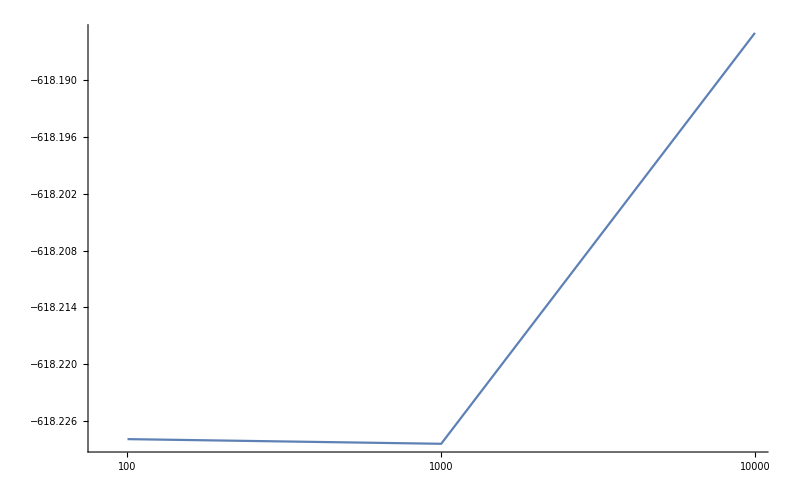

```mathematica
UVTest = With[{(*λA=1,*) pEval = 10^2, μ=2, αs = 22/100, λmin=10^-2},Table[{Λ,NIntegrate[λIntRenVec[pEval,αs,λA,λ,μ],{λA,10^-2,10},{λ,λmin,Λ},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,PrecisionGoal->3]},{Λ,UVCutoffs}]]
ListLogLinearPlot[Re[UVTest],Joined ->True, ImageSize->800]
```

```mathematica
ρ1Test = %2470
```

InterpolatingFunction[…]

```mathematica
ρ1Test
```

ρ1Test

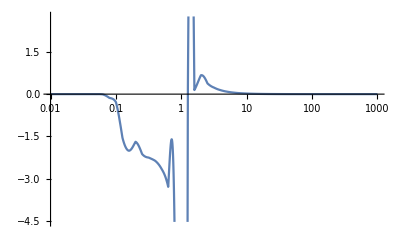

```mathematica
LogLinearPlot[ρ1Test[λ],{λ,0.01,1000.}]
```

### Plot quark wave function renormalization Z (p)

From this expression we can extract the quark wave function renormalization as:

```mathematica
Zq[p_,αs_,λA_,λ_,μ_]:= 1/(1-1/24*IVecRenE[p,αs,λA,λ,μ]) (*The factor 24 comes from the respective traces of δ^(ab) (=8) and the transversal projection operator (=3)*)
```

```mathematica
With[{μ=2, αs = 9.6^2/(4π), λA=1.4, λ=0.13},Plot[{Zq[p,αs,λA,λ,μ]},{p,0.01,0.5*10^1},WorkingPrecision->100, ImageSize->800,PlotRange->All]] (*values for masses and coupling from Paris paper*)
```

### Check if the analytic continuation of the whole diagram works

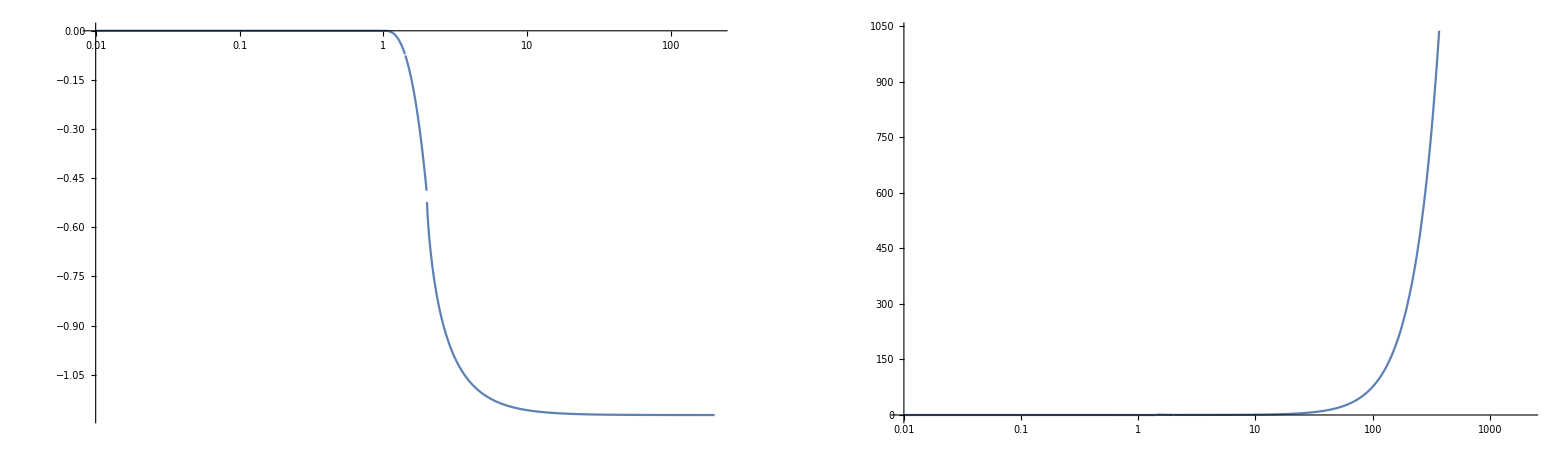

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[IVecRenE[-I(ω+I*10^-9),22/100,1,1,2]](*,Evaluate[Im[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]*)},{ω,10^-2,2*10^2},WorkingPrecision->30],LogLinearPlot[{Re[IVecRenE[-I(ω+I*10^-9),22/100,1,1,2]](*,Evaluate[Re[IVecRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]*)},{ω,10^-2,2*10^3},WorkingPrecision->30]},ImageSize->1600]]
```

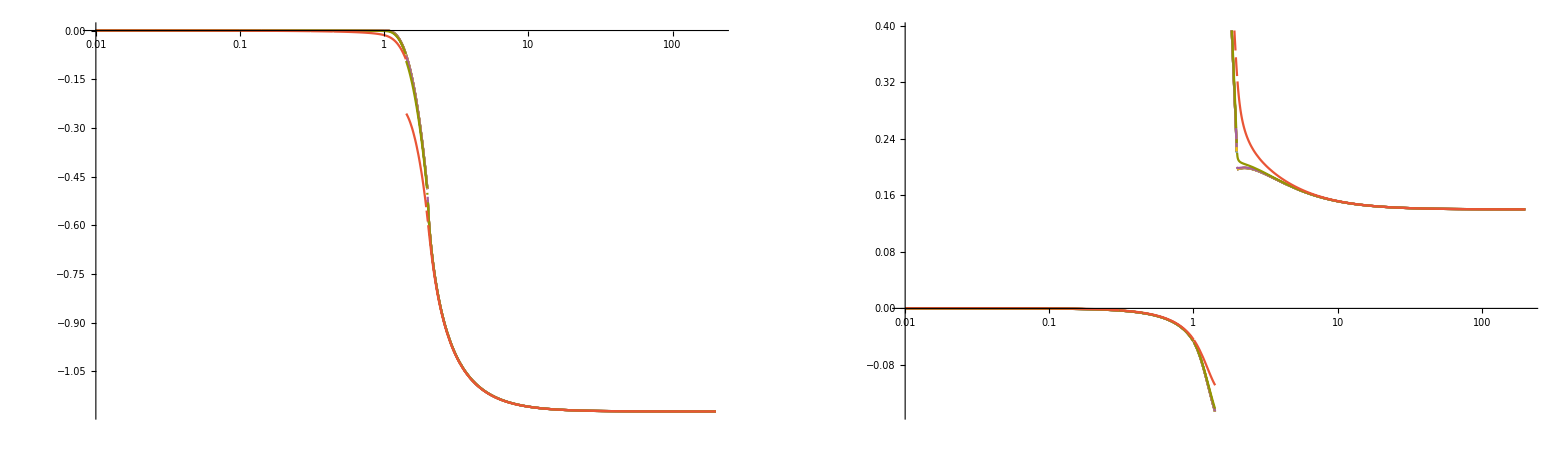

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[IVecCont[ω,22/100,1,1,2]],Evaluate[Im[IVecE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,2*10^2},WorkingPrecision->30],LogLinearPlot[{Re[IVecCont[ω,22/100,1,1,2]],Evaluate[Re[IVecE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,2*10^2},WorkingPrecision->30]},ImageSize->1600]]
```

## Dirac Scalar Part -> B(p^2)

### Collecting coefficients

```mathematica
(*scalar part*)
C0[p_,λA_,x_] := 3
C1[p_,λA_,x_] := 0

CScal[p_,λA_,x_]:={C0[p,λA,x],C1[p,λA,x]}
```

### Feynman Parameter Integrals -> already computed above

```mathematica
h0[p_,λA_,λ_] := -2+Log[λ]+1/p^2(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) ArcCoth[(p^2+λ^2+λA^2)/(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))]+(-λ^2+λA^2) Log[λ/λA])+Log[λA]
h[p_,λA_,λ_] := {h0[p,λA,λ]}
```

```mathematica
γ0[p_,λA_,λ_]:=Evaluate[FullSimplify[(C0[p,λA,x])/.x->0]] (*higher terms not present!!*)
γ[p_,λA_,λ_] := {γ0[p,λA,λ]}
```

```mathematica
γ0[p,λA,λ]
```

3

### Realtime expressions

```mathematica
h0Logs[p_,λA_,λ_] := -2+Log[λ]+ Log[λA] +1/(2 p^2)(√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4) (Log[1+1/((p^2+λ^2+λA^2)/√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))] - Log[1-1/((p^2+λ^2+λA^2)/√((p^2+λ^2)^2+2 (p-λ) (p+λ) λA^2+λA^4))] )+2(-λ^2+λA^2) Log[λ/λA])
```

```mathematica
h0cont[ω_,λA_,λ_] := h0[-I*ω, λA,λ]
```

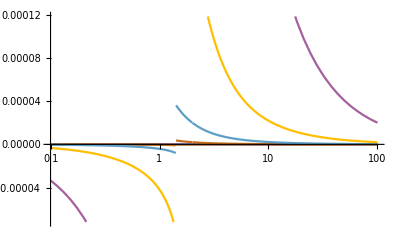

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[h0cont[ω,1,1]],Evaluate[Im[h0Logs[-ⅈ(ω+ⅈ*#),1,1]]&/@ε]},{ω,10^-1,10^2},WorkingPrecision->30]},ImageSize->800]]
```

### BPHZ Renormalization + Visualization

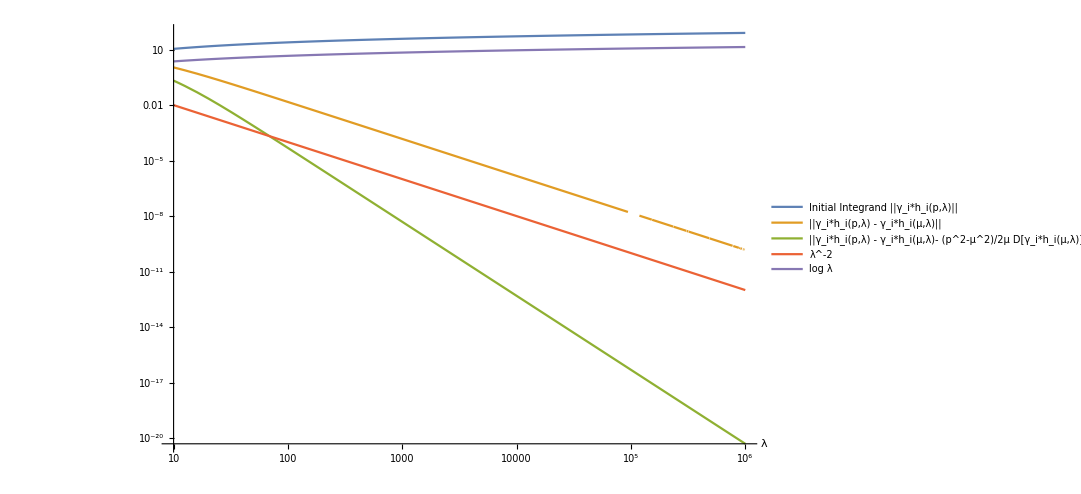

```mathematica
With[{λA=1, μ=10,pEval=1, i=1},LogLogPlot[{Abs[γ[pEval,λA,λ][[i]]h[pEval,λA,λ][[i]]],Abs[γ[pEval,λA,λ][[i]]h[pEval,λA,λ][[i]] - γ[μ,λA,λ][[i]]h[μ, λA,λ][[i]]],Abs[γ[pEval,λA,λ][[i]]h[pEval,λA,λ][[i]] - γ[μ,λA,λ][[i]]h[μ, λA,λ][[i]]-((pEval^2-μ^2)/2/μ)(D[γ[q,λA,λ][[i]]h[q, λA,λ][[i]],q]/.{q->μ})], λ^-2,  Log[λ]},{λ,10^1,10^6},WorkingPrecision->100, ImageSize->800 , PlotLegends->{"Initial Integrand ||γ_i*h_i(p,λ)||", "||γ_i*h_i(p,λ) - γ_i*h_i(μ,λ)||", "||γ_i*h_i(p,λ) - γ_i*h_i(μ,λ)- (p^2-μ^2)/2μ D[γ_i*h_i(μ,λ)] ||","λ^-2","log λ"}, AxesLabel->{"λ"}]]
```

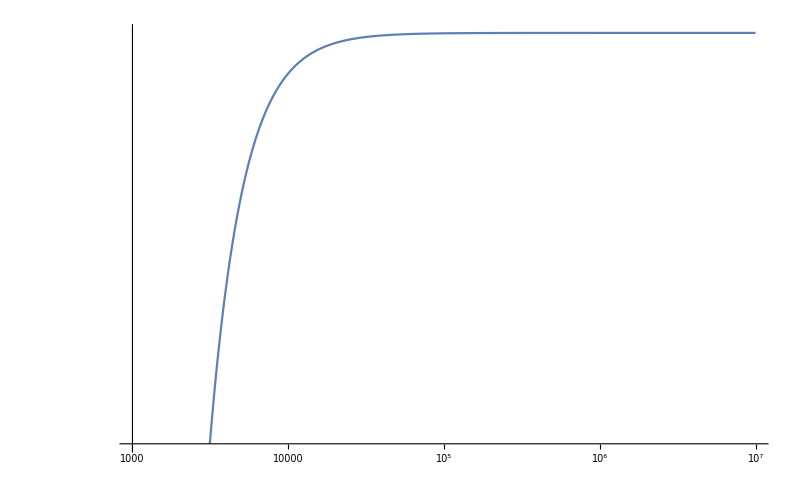

```mathematica
With[{λA=1, μ=100,pEval=1, i=1},LogLogPlot[{(Abs[γ[pEval,λA,λ][[i]]h[pEval,λA,λ][[i]] - γ[μ,λA,λ][[i]]h[μ, λA,λ][[i]]])*λ^2},{λ,10^3,10^7},WorkingPrecision->150, ImageSize->800]]
```

```mathematica
γhRen[p_,λA_,λ_,μ_] := {γ0[p,λA,λ]h0[p,λA,λ]-γ0[μ,λA,λ]h0[μ,λA,λ]}
```

```mathematica
λIntRenTestScal[pEval_,λA_, λ_, μ_,i_] :=  λ*ρ12UV[λ]* γhRen[pEval, λA,λ,μ][[i]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {4.6873275401546402431723945569203223768989789576319291532530653371964624705867672}. NIntegrate obtained -3.8525919177947413689550386551350015240430427007621712972816473328073382019434634 and 8.4841348462056511249640473958317709649927372626550310581012475812272769374557106×10^-16 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{100,3.80762674669042904235793955541},{1000,3.84809915924112688895477557568},{10000,3.85214911784989508266530733772},{100000,3.85255411779470211853027748068},{1000000,3.85256311779718909399775428816},{10000000,3.85259191779474136895503865514},{100000000,0}}

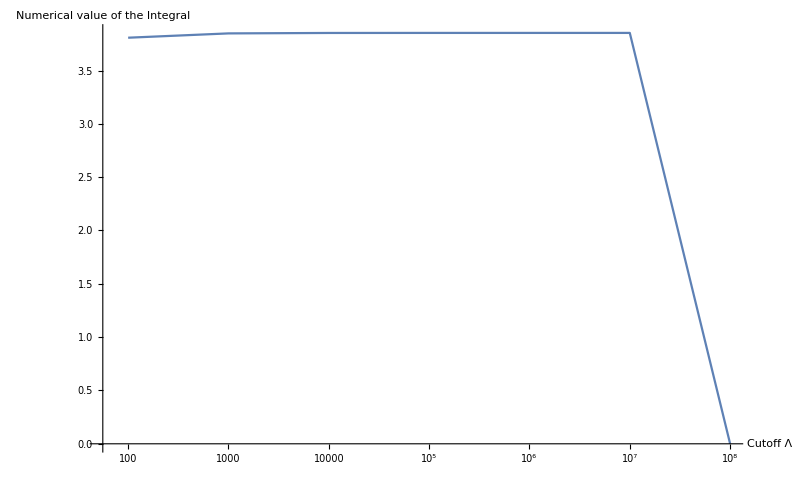

```mathematica
UVTestScal = With[{λA=1, pEval = 1, μ=2, i=1, λmin=10^-2},Table[{Λ,-NIntegrate[λIntRenTestScal[pEval,λA,λ,μ,i],{λ,λmin,Λ}, WorkingPrecision->30]},{Λ,UVCutoffs}]]
ListLogLinearPlot[UVTestScal,Joined ->True, ImageSize->800, AxesLabel->{"Cutoff Λ","Numerical value of the Integral"},PlotLabel->None,LabelStyle->{14}]
```

### Complete Diagram (Scalar)

```mathematica
IScalE[p_,αs_,λA_,λ_,μ_]:=-(32*αs)/(4π)(Log[4π*μ^2Exp[-EulerGamma]]*γ0[p,λA,λ]-γ0[p,λA,λ]*h0[p,λA,λ])
IScalCont[ω_,αs_,λA_,λ_,μ_]:=-(32*αs)/(4π)(Log[4π*μ^2Exp[-EulerGamma]]*γ0[-I*ω,λA,λ]-γ0[-I*ω,λA,λ]*h0[-I*ω,λA,λ])
DIScalE[p_,αs_,λA_,λ_,μ_]:= Evaluate[D[IScalE[p,αs,λA,λ,μ],p]]
```

Renormalized Integrand :

```mathematica
IScalRenE[p_,αs_,λA_,λ_,μ_]:= IScalE[p,αs,λA,λ,μ] - IScalE[μ,αs,λA,λ,μ] (*- ((p^2-μ^2)/2/μ)(D[IScalE[q,αs,λA,λ,μ],q]/.{q->μ})*)
```

```mathematica
λIntRenScal[pEval_,αs_,λA_, λ_, μ_] :=  λ*ρ12UV[λ]*IScalRenE[pEval,αs, λA,λ,μ]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.0100019051697813577836388625042380958298923593206346976078630943719455995886942025548466161340386410203141048965891742750497548465304470474705445617411}. NIntegrate obtained -2.13312921601012221560606128579917241681150052648646675633036142512122408305650660940923780449914905563754988958125443682351417389757529264191869633087 and 4.2434807699046551362345945627163610695165676543378695931508281664708220165856544335779407021263771271974453717483133391120278941508140466286415220881×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {4.69906550212769084400017089750715310947600866530113436882738517633908617329219357207073253098350154152052194371494134288612626794933623974467892282981}. NIntegrate obtained -2.15832362848525845142273895572788819490051801839252066568721695963320998417718009437260859062306935973066376955272885309869157066400692973174211179017 and 1.32141428034767159446820574820284370832880325665417668984779415161858161643558582215417166571389745007013378247213844145249475084845196123116816765576×10^-52 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {0.01}. NIntegrate obtained -2.158323855376545323174612946778807877620810569379866206315956187061374231573778720172848175925534904 and 2.066048474433631841624899482634639115142750095494715958567050270160576012080400288790904979621625567×10^-80 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{100,-2.133129216010122215606061285799172416811500526486466756330361425121224083056506609409237804499149056},{1000,-2.15580288950749126827381129934777111020874668313127293406089130183540840405874506211627790252376552},{10000,-2.158071779187789946110793773467455329971011640024139091726011414913739698397552147924995635868765675},{100000,-2.158298670443741251709203280115698428255383214189581837710604571131953432052187655567229514964495716},{1000000,-2.158321359572389779747453180003278227906772564661774461796158635726658285640829756672152121885370365},{10000000,-2.15832362848525845142273895572788819490051801839252066568721695963320998417718009437260859062306936},{100000000,-2.158323855376545323174612946778807877620810569379866206315956187061374231573778720172848175925534904}}

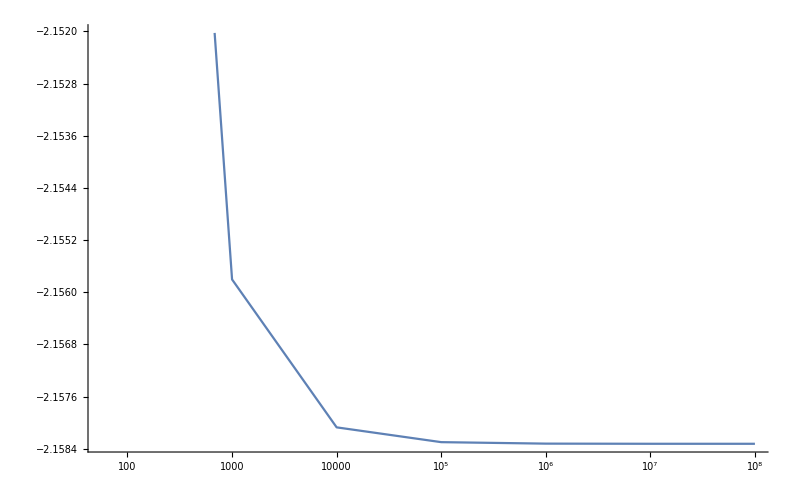

```mathematica
UVTest = With[{λA=1, pEval = 1, μ=2, αs = 22/100, λmin=10^-2},Table[{Λ,NIntegrate[λIntRenScal[pEval,αs,λA,λ,μ],{λ,λmin,Λ}, WorkingPrecision->100]},{Λ,UVCutoffs}]]
ListLogLinearPlot[UVTest,Joined ->True, ImageSize->800]
```

#### Check if the analytic continuation of the whole diagram works

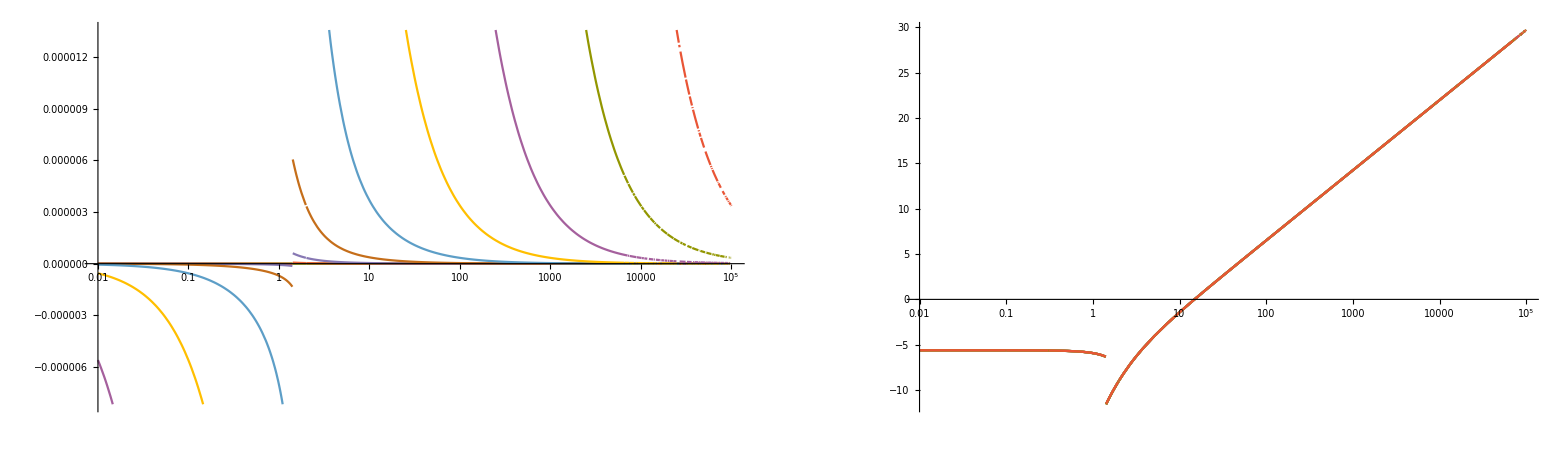

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[IScalCont[ω,22/100,1,1,2]],Evaluate[Im[IScalE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30],LogLinearPlot[{Re[IScalCont[ω,22/100,1,1,2]],Evaluate[Re[IScalE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30]},ImageSize->1600]]
```

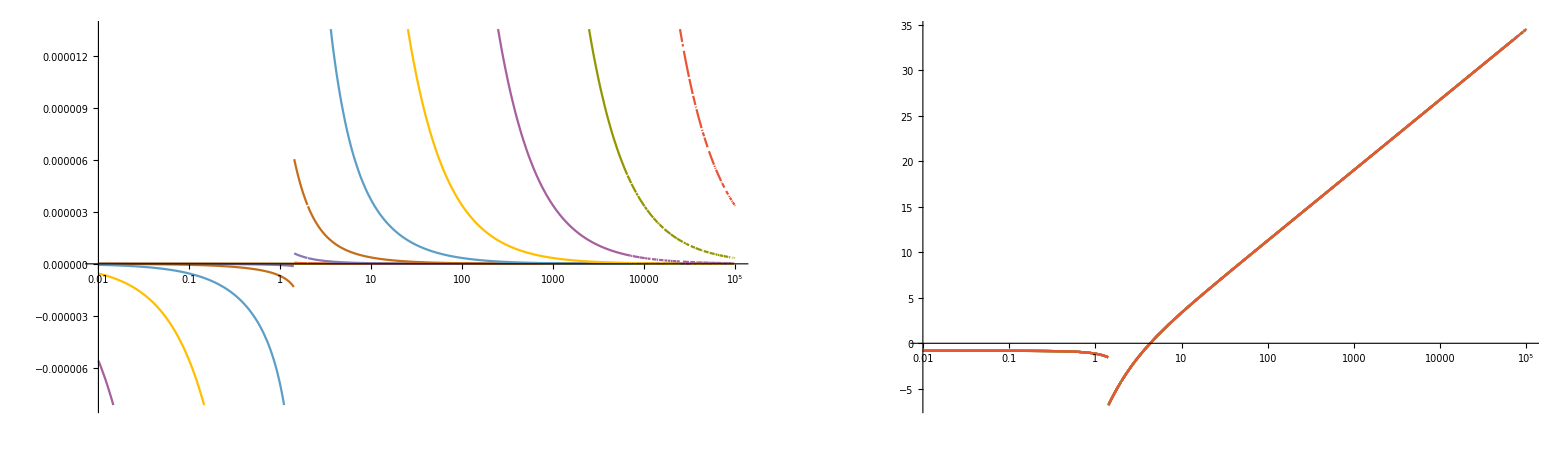

```mathematica
With[{ε=10^Range[-10,-1]},GraphicsRow[{LogLinearPlot[{Im[IScalRenE[-I*ω,22/100,1,1,2]],Evaluate[Im[IScalRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30],LogLinearPlot[{Re[IScalRenE[-I*ω,22/100,1,1,2]],Evaluate[Re[IScalRenE[-I(ω+I*#),22/100,1,1,2]]&/@ε]},{ω,10^-2,10^5},WorkingPrecision->30]},ImageSize->1600]]
```

this sign flip is a characteristic of the logarithm -> no problem!

### Plot first result the quark mass function M(p)

As before, we can now define the quark mass function M(p) as the ratio of the terms proportional to the respective parts of the diagram.

```mathematica
Mq[p_,αs_,λA_,λ_,μ_]:=(1-1/24*IScalE[p,αs,λA,λ,μ])/(1-1/24*IVecE[p,αs,λA,λ,μ]) (*discuss possible factor of Lambda coming from the classical spectral function, cf. tex-document*)
```

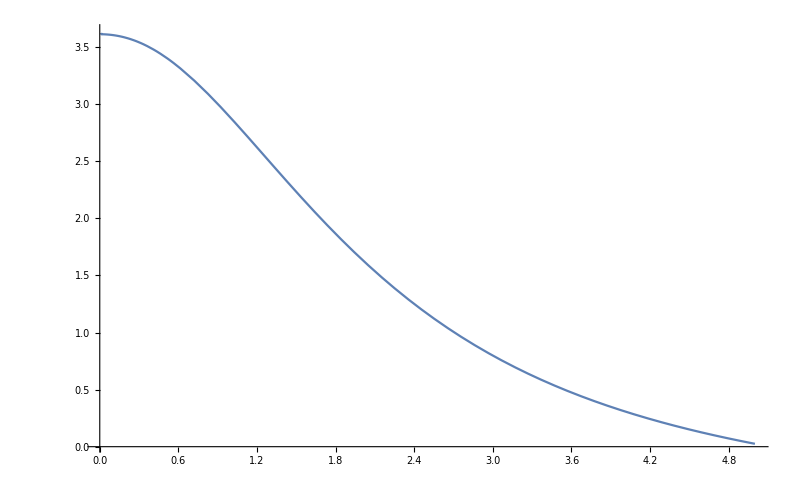

```mathematica
With[{μ=2, αs = 9.6^2/(4π), λA=1.4, λ=0.13},Plot[{Mq[p,αs,λA,λ,μ]},{p,10^-2,0.5*10^1},WorkingPrecision->30, ImageSize->800,PlotRange->All]]
```

We use the terms presented in the Paris paper :

```mathematica
Q[p_, m_, M_] := Log[((Sqrt[m^4+2*m^2*(p^2-M^2)+(M^2+p^2)^2]-p^2)^2 - (M^2-m^2)^2)/((Sqrt[m^4+2*m^2*(p^2-M^2)+(M^2+p^2)^2]+p^2)^2 - (M^2-m^2)^2)]
kSquared[p_, m_, M_] :=  Sqrt[m^4 + 2m^2(p^2-M^2) + (M^2+p^2)^2]
```

```mathematica
pSlashedPerturb[αs_,p_,m_,M_] := -(4/3)αs/(16*Pi*m^2p^4)(kSquared[p, m, M](2m^4 + m^2(p^2-M^2) - (M^2+p^2)^2)Q[p, m, M]-2m^2p^2(-2m^2 + M^2+p^2) - 2(2m^6 + 3m^4(p^2-M^2) +(p^2+M^2)^3)Log[M/m] - 2(M^2 + p^2)^3Log[(M^2+p^2)/M^2])
```

```mathematica
IdPerturb[αs_,p_,m_,M_] :=(4/3)αs(3M/(2*Pi))(Log[m*Exp[-EulerGamma]/Sqrt[4*Pi]]-(2/3) - kSquared[p, m, M] * Q[p, m, M]/(4p^2) + 1/(2p^2)(m^2-M^2+p^2)Log[M/m])
```

### Plots

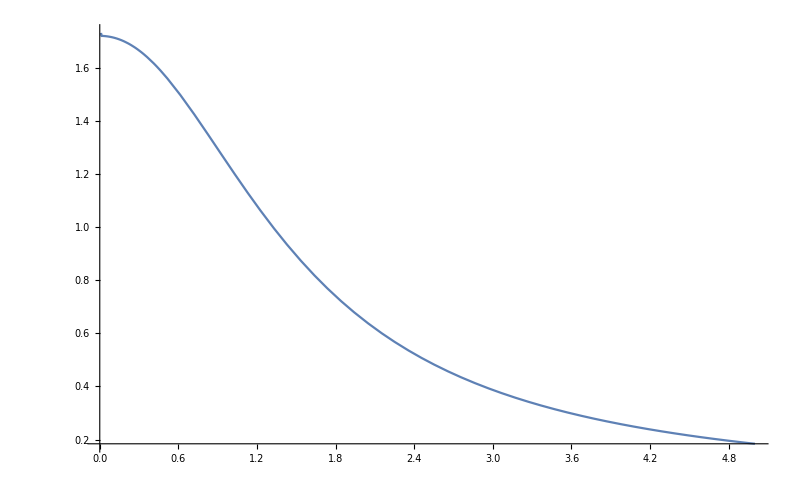

```mathematica
With[{ μ=2, αs = (9.6^2)/(4π), m= 1.4, M=0.13},Plot[{(*1/(1-(1/24)*pSlashedPerturb[αs, p,m,M]),*) Zq[p,αs,m,M,μ]},{p,0.01,0.5*10^1},WorkingPrecision->30, ImageSize->800,PlotRange->All]]
```

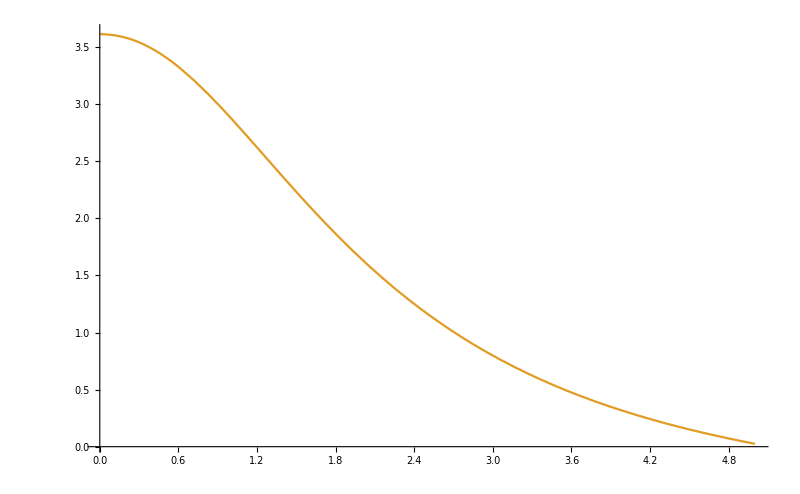

```mathematica
With[{ μ=2, αs = 9.6^2/(4π), m= 1.4, M=0.13},Plot[{(*(1-IdPerturb[αs, p,m,M])/(1-pSlashedPerturb[αs, p,m,M])*), Mq[p,αs,m,M,μ] },{p,0.01,5},WorkingPrecision->100, ImageSize->800,PlotRange->All]]
```